```mathematica
Clear["Global`*"];
(* All in mkm *)
```

```mathematica
dCore=8.2;
NA=0.14;
λ=1.55;
nMat=1.45;
β0=(2Pi nMat)/λ;
α=-0.01;
αTest=-0.7;
```

```mathematica
CalcWindow=50;
N0=255;
h=0.05;
```

```mathematica
n[r_]:=Piecewise[{{N[√(nMat^2+NA^2)],0≤r<dCore/2},{N[nMat],dCore/2≤r<2dCore},{N[√(nMat^2+α I)],1.5dCore≤r}}]
{Plot[Re[n[r]],{r,0,CalcWindow},ImageSize->Medium,Exclusions->None],Plot[Im[n[r]],{r,0,CalcWindow},ImageSize->Medium,Exclusions->None]};
```

```mathematica
R=dCore/2;
GaussR[r_]:=N[Exp[-(r/R)^2]];
SuperGaussR[r_]:=N[Exp[-(r/R)^4]];
StepR[r_]:=Piecewise[{{1.,0≤r^2<R^2},{0,r^2≥R^2}}];
```

```mathematica
nArr=Array[n[√(#1^2+#2^2)]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
StartBeam=Array[StepR[√(#1^2+#2^2)]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
FourierStartBeam=RotateLeft[Fourier[StartBeam],{(N0+1)/2,(N0+1)/2}];
```

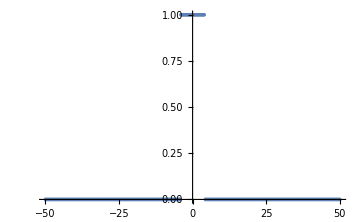
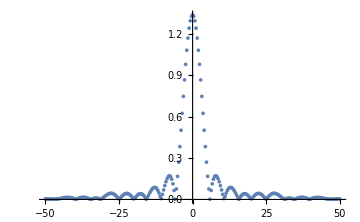
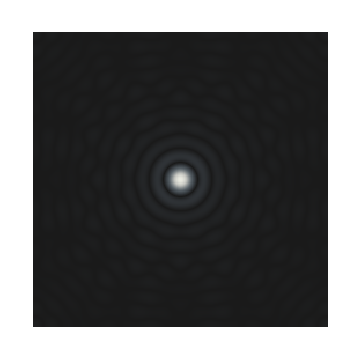

```mathematica
{ListPlot[Abs[StartBeam[[(N0+1)/2]]],
Joined->False,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ImageSize->Medium],
ListPlot[Abs[FourierStartBeam[[(N0+1)/2]]],
Joined->False,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ImageSize->Medium],
ArrayPlot[Abs[FourierStartBeam],DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium]
}
```

```mathematica
{ArrayPlot[Abs[StartBeam]^2,DataRange->{{-dCore/2,dCore/2},{-dCore/2,dCore/2}},ColorFunction->"GrayTones",ImageSize->Medium],
ListPlot[Abs[StartBeam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{{-dCore,dCore},All},ImageSize->Medium]};
```

```mathematica
D2Fourier=(π/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp=Exp[I (D2Fourier h)/(2β0)];
SqrtFourierOp=√FourierOp;
SpatialOp=Exp[-I ((2 π)/λ)^2 ((nArr^2-nMat^2) h)/(2β0)];
```

```mathematica
L=10000 h;
```

```mathematica
Beam=StartBeam;
```

```mathematica
Monitor[
ξ="Starting";
Beam=InverseFourier[SqrtFourierOp Fourier[Beam]];
For[ξ=0.5h,ξ<L,ξ+=h,
Beam=InverseFourier[FourierOp Fourier[Beam SpatialOp]];
];
ξ="Finishing";
Beam=InverseFourier[Fourier[Beam]/SqrtFourierOp],
{If[NumberQ[ξ] ,ToString[Round[(1000ξ)/L]×0.1]<>"%",ξ]
,ListPlot[Abs[Beam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{{-CalcWindow,CalcWindow},All},ImageSize->Medium]
,ListPlot[Abs[Beam[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{{-CalcWindow,CalcWindow},All},ImageSize->Medium]}];
```

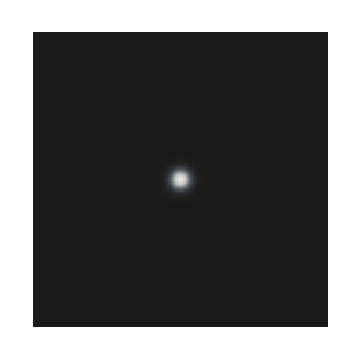
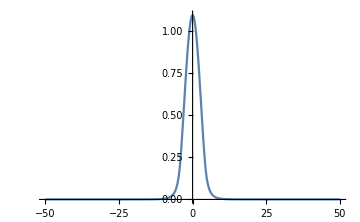
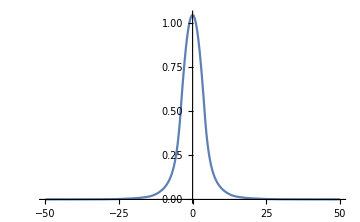

```mathematica
{ArrayPlot[Abs[Beam]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium]
,ListPlot[Abs[Beam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ImageSize->Medium]
,ListPlot[Abs[Beam[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ImageSize->Medium]}
```